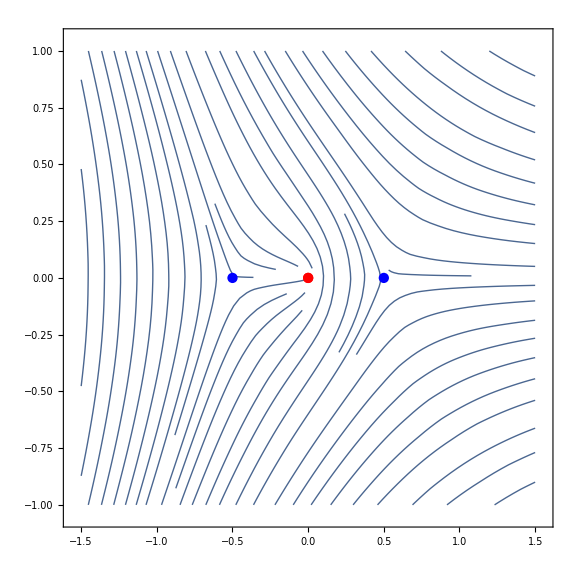
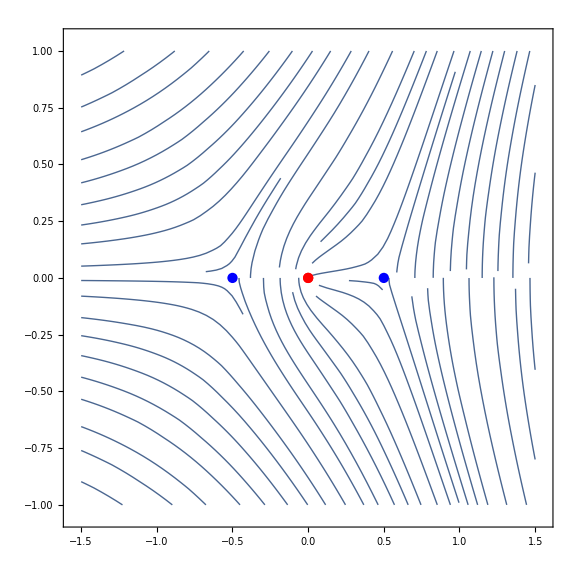

```mathematica
β=0.5;
potential=Function[x,-x+β^2/x];
StokesGraph[potential,1]
Clear[β,potential];
```

```mathematica
F=({{ⅇ^i, 0}, {r ⅇ^i, ⅇ^-i}});(*r->b+aⅇ^(-2i),F=S[b].W[i].S[a]*)
P=S[ⅈ p]ᵀ;
F.{1,0};
%⟦2⟧/%⟦1⟧//Simplify
F*.P.{1,0};
%⟦1⟧/%⟦2⟧//Simplify
```

r

1/Conjugate[r]

```mathematica
Inverse[J.F*.J]*.F*.P.{1,0};
(J.P*.J).Inverse[J.F*.J].F.{1,0}/.p*->p;
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦1⟧ⅇ^(4/3 ρ^(3/2))+%%⟦2⟧), 1, (Log[ρ]+2π ⅈ)}, {ⅈ(%⟦1⟧ⅇ^(4/3 ρ^(3/2))+%⟦2⟧), 1, (Log[ρ]-2π ⅈ)}})//Det//Simplify//Apart;
D[%,ρ]/(2 √ρ)ⅇ^(-4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(4/3 ρ^(3/2))//Simplify

Inverse[J.F*.J]*.F*.P.{0,1};
(J.P*.J).Inverse[J.F*.J].F.{0,1}/.p*->p;
({{1, 1, Log[ρ]}, {-ⅈ(%%⟦1⟧+%%⟦2⟧ⅇ^(-4/3 ρ^(3/2))), 1, (Log[ρ]+2π ⅈ)}, {ⅈ(%⟦1⟧+%⟦2⟧ⅇ^(-4/3 ρ^(3/2))), 1, (Log[ρ]-2π ⅈ)}})//Det//Simplify//Apart;
-D[%,ρ]/(2 √ρ)ⅇ^(4/3 ρ^(3/2))//Simplify
%%-%ⅇ^(-4/3 ρ^(3/2))//Simplify
```

0

2 π (-2 ⅈ+ⅈ ⅇ^(i+Conjugate[i]) p-ⅇ^(i-Conjugate[i]) r+ⅇ^(-i+Conjugate[i]) (1-ⅈ ⅇ^(2 i) p r) Conjugate[r])

0

2 π (-2 ⅈ+ⅈ ⅇ^(i+Conjugate[i]) p-ⅇ^(i-Conjugate[i]) r+ⅇ^(-i+Conjugate[i]) (1-ⅈ ⅇ^(2 i) p r) Conjugate[r])

```mathematica
ρ^2+2ρ Sin[ϕ+2Im[i]] ⅇ^(-2 Re[i])/p +(2 ⅇ^(-2 Re[i])/p -1)==0;
Solve[ρ^2+2ρ Sin[ϕ+2Im[i]] ⅇ^(-2 Re[i])/p +(2 ⅇ^(-2 Re[i])/p -1)==0,ρ]
```

{{ρ→1/2 (-(2 ⅇ^(-2 Re[i]) Sin[ϕ+2 Im[i]])/p-√(4-(8 ⅇ^(-2 Re[i]))/p+(4 ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2)/p^2))},{ρ→1/2 (-(2 ⅇ^(-2 Re[i]) Sin[ϕ+2 Im[i]])/p+√(4-(8 ⅇ^(-2 Re[i]))/p+(4 ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2)/p^2))}}

```mathematica
Integrate[ⅈ √((1-x^2)/x)ⅈ x/.x->ⅇ^(ⅈ ϕ),{ϕ,0,-π}]
```

((1-ⅈ) √π Gamma[5/4])/Gamma[7/4]

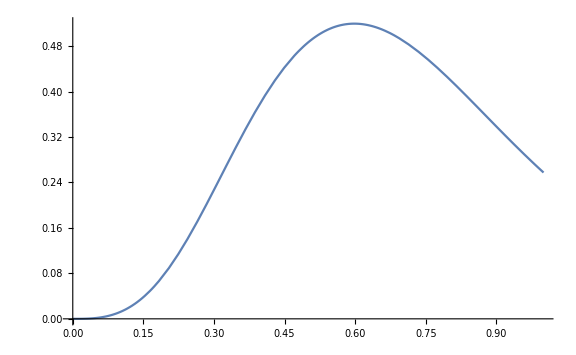

```mathematica
Plot[1-ρ^2/.ρ->(ⅇ^(-2 Re[i]) (-2 Cosh[2 Im[i]]+√2 √(1-4 ⅇ^(2 Re[i]) p+2 ⅇ^(4 Re[i]) p^2+Cosh[4 Im[i]])))/(2 p)/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2)/.p->2/3 ⅇ^(β^(3/2))(1-ⅇ^(β^(3/2))),{β,0,1},PlotRange->Full,ImageSize->Large]
```

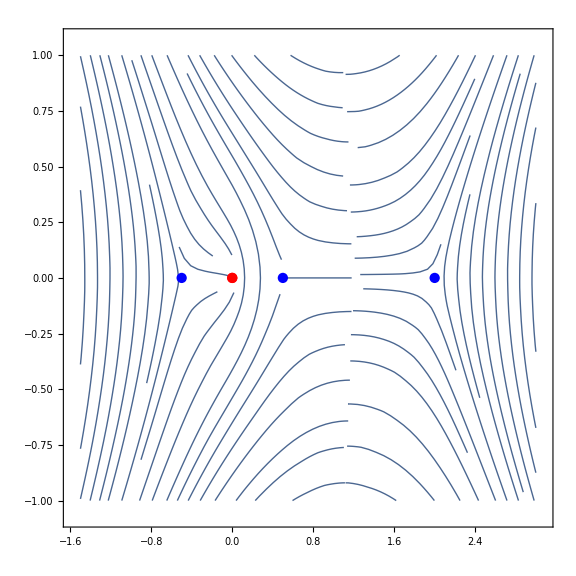
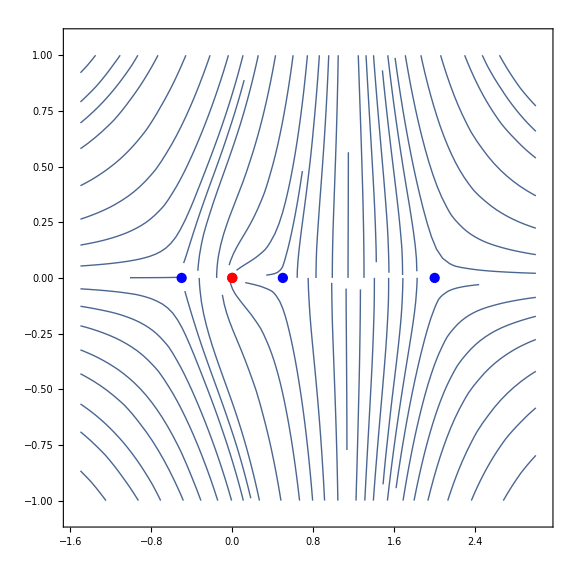

```mathematica
β=0.5;l=2;
potential=Function[x,(β^2-x^2)/x(1-x/l)];
StokesGraph[potential,1]
Clear[β,l,potential];
```

```mathematica
S[b]ᵀ.W[-i].S[a]ᵀ.W[-L].S[c]//Simplify//MatrixForm
```

(ⅇ^(-i-L)+a c ⅇ^(-i+L)+b c ⅇ^(i+L) | ⅇ^(-i+L) (a+b ⅇ^(2 i))
c ⅇ^(i+L) | ⅇ^(i+L))

```mathematica
F=({{ⅇ^(-i-L)+c r ⅇ^(i+L), r ⅇ^(i+L)}, {c ⅇ^(i+L), ⅇ^(i+L)}});(*r->b+aⅇ^(-2i),c->-ⅈ,F=S[b]ᵀ.W[-i].S[a]ᵀ.W[-L].S[с]*)
F.{1,0};
1-Abs[%⟦1⟧/%⟦2⟧]^2-Abs[1/%⟦2⟧]^2//Simplify
J.F*.J.{1,0};
1-Abs[%⟦1⟧/%⟦2⟧]^2-Abs[1/%⟦2⟧]^2//Simplify
```

1-ⅇ^(-2 Re[i+L])/Abs[c]^2-ⅇ^(-2 Re[i+L]) Abs[ⅇ^(-i-L)/c+ⅇ^(i+L) r]^2

-(1+ⅇ^(-2 Re[i+L])-Abs[r]^2)/Abs[r]^2

```mathematica
Limit[ⅇ^(-2 Re[i+L]) (-1+ⅇ^(2 Re[i+L])-Abs[ⅇ^(-i-L)-ⅈ ⅇ^(i+L) r]^2),L->Infinity]
Limit[-(1+ⅇ^(-2 Re[i+L])-Abs[r]^2)/Abs[r]^2,L->Infinity]
```

1-Im[r]^2-Re[r]^2

1-1/Abs[r]^2

```mathematica
Inverse[F].(J.F*.J).{1,0}/.(i+L)*->(i*+L)/.L*->L//Simplify//MatrixForm
```

```mathematica
({{ⅇ^(2Re[i]+2 L) a}, {-a c ⅇ^(2Re[i]+2L) +Conjugate[r] ⅇ^(-2ⅈ Im[i])}})
```

```mathematica
Inverse[J.F*.J].F.{1,0}/.(i+L)*->(i*+L)/.L*->L//Simplify//MatrixForm
```

```mathematica
({{-(ⅇ^(2Re[i]+L) Abs[c]^2 a-ⅇ^(-2Re[i]-2L)-c*r*ⅇ^(-2ⅈ Im[i])-c r ⅇ^(2ⅈ Im[i]))}, {c ⅇ^(2 Re[i]+2L)a-Conjugate[r] ⅇ^(-2ⅈ Im[i])}})
```

```mathematica
({{ⅇ^(2Re[i]+2 L) a}, {-a c ⅇ^(2Re[i]+2L) +Conjugate[r] ⅇ^(-2ⅈ Im[i])}});
({{-(ⅇ^(2Re[i]+2L) Abs[c]^2 a-ⅇ^(-2Re[i]-2L)-c*r*ⅇ^(-2ⅈ Im[i])-c r ⅇ^(2ⅈ Im[i]))}, {c ⅇ^(2 Re[i]+2L)a-Conjugate[r] ⅇ^(-2ⅈ Im[i])}});
({{1, 1, Log[ρ]}, {-(%%⟦1⟧+%%⟦2⟧ⅇ^(-ⅈ 2 ρ^2)), 1, (Log[ρ]+2π ⅈ)}, {-(%⟦1⟧+%⟦2⟧ⅇ^(-ⅈ 2 ρ^2)), 1, (Log[ρ]-2π ⅈ)}})/.(i+L)*->(i*+L)/.L*->L//Det//Simplify//Apart;
D[%,ρ]/(-4ⅈ ρ)ⅇ^(ⅈ 2 ρ^2)//Simplify
%%-%ⅇ^(-ⅈ 2 ρ^2)//Simplify
```

0

-2 ⅈ π (2+ⅇ^(-2 (L+Re[i]))+a ⅇ^(2 (L+Re[i]))+c ⅇ^(2 ⅈ Im[i]) r-a ⅇ^(2 (L+Re[i])) Abs[c]^2+ⅇ^(-2 ⅈ Im[i]) Conjugate[c] Conjugate[r])

```mathematica
2+ⅇ^(-2 Re[i]-2L)+a ⅇ^(2Re[i]+2 L)(1-Abs[c]^2)+c r ⅇ^(2 ⅈ Im[i])+c*r*ⅇ^(-2 ⅈ Im[i])
```

```mathematica
Solve[ρ^2+2ρ Sin[2Im[i]+ ϕ] ⅇ^(-2Re[i])+(2 ⅇ^(-2Re[i])-1)==0,ρ]
```

{{ρ→1/2 (-2 ⅇ^(-2 Re[i]) Sin[ϕ+2 Im[i]]-√(4-8 ⅇ^(-2 Re[i])+4 ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2))},{ρ→1/2 (-2 ⅇ^(-2 Re[i]) Sin[ϕ+2 Im[i]]+√(4-8 ⅇ^(-2 Re[i])+4 ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2))}}

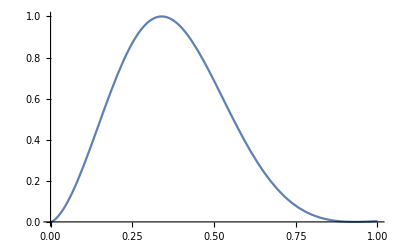

```mathematica
Plot[1-ρ^2/.ρ->-Sin[ϕ+2 Im[i]] ⅇ^(-2 Re[i])-√(1-2 ⅇ^(-2 Re[i])+ⅇ^(-4 Re[i]) Sin[ϕ+2 Im[i]]^2)/.ϕ->-π/2/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2),{β,0,1},PlotRange->Full]
```

```mathematica
ρ^2+2ρ Sin[ϕ+2Im[i]] ⅇ^(-2 Re[i])/p +(2 ⅇ^(-2 Re[i])/p -1)==0;
ρ^2+2ρ Sin[ϕ+2Im[i]] ⅇ^(-2 Re[i]) +(2 ⅇ^(-2 Re[i]) -1)==0;
```

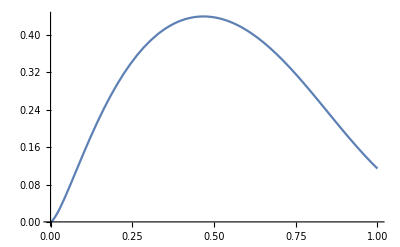

```mathematica
Plot[2 ⅇ^(-2Re[i])((1-s^2 ⅇ^(-2Re[i]))+s √(1-ⅇ^(-2Re[i])(2-s^2 ⅇ^(-2Re[i]))))/.s->Sin[ϕ+2Im[i]]/.ϕ->-π/2/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2),{β,0,1},PlotRange->Full]
```

```mathematica
2(√π Gamma[5/4])/Gamma[7/4]//N
```

3.49608

```mathematica
dissFunc=Interpolation[βDissipation];
```

```mathematica
Solve[2 ⅇ^(-2Re[i])((1-s^2 ⅇ^(-2Re[i]))+s √(1-ⅇ^(-2Re[i])(2-s^2 ⅇ^(-2Re[i]))))==a,s]
```

{{s→-(ⅈ (-2+a ⅇ^(2 Re[i])))/(√(-4+4 a))},{s→(ⅈ (-2+a ⅇ^(2 Re[i])))/(√(-4+4 a))}}

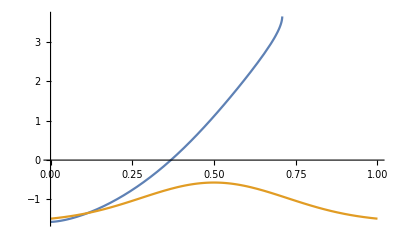

```mathematica
Plot[{(ArcSin[-(2-a ⅇ^(2 Re[i]))/(2 √(1- a))]-2Im[i])/.i->((1-ⅈ) √π Gamma[5/4])/Gamma[7/4] β^(3/2)/.a->dissFunc[β],-π/2+ⅇ^(-10(β-0.5)^2)},{β,0,1},PlotRange->All]
```

```mathematica
GetR[extQ_,extk_,intvl_,init_]:=
Module[{Q,k,M,r,x,externalSymbol,localVar,a,b},
externalSymbol=Unevaluated[intvl]/.{x_,y__}:>HoldPattern[x];
Q=Unevaluated[extQ]/.externalSymbol:>localVar;
k=Unevaluated[extk]/.externalSymbol:>localVar;
{a,b}=Rest[intvl];

M=Inverse[({{1, 1}, {ⅈ k, -ⅈ k}})].(({{0, 1}, {-Q, 0}}).({{1, 1}, {ⅈ k, -ⅈ k}})-D[({{1, 1}, {ⅈ k, -ⅈ k}}),localVar]);
r=NDSolveValue[{D[x[localVar],localVar]==-(M⟦1,2⟧x[localVar]^2+(M⟦1,1⟧-M⟦2,2⟧)x[localVar]-M⟦2,1⟧),x[a]==init},x,{localVar,a,b}];
r
];
```

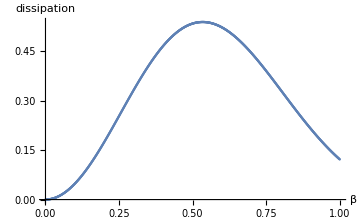

```mathematica
(*TEM dissipation for X-wave*)
βDissipation={};
α=10^-5;l=20;
βbegining=0;βend=1;βnstep=1000;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)]]
For[β=βbegining,β≤βend,β+=(βend-βbegining)/βnstep,
r=GetR[(β^2-z^2)/z/.{z->z-ⅈ α},ⅈ √(z-ⅈ α),{z,l,-l},0];
βDissipation=Append[βDissipation,{β,1-Abs[r[-l]]^2}];
];
ListPlot[βDissipation,PlotRange->Full,AxesLabel->{"β","dissipation"},ImageSize->Medium]
(*SaveData[config["isotropism","data"],δDissipation]*)
Clear[α,l,β,βbegining,βend,βnstep,r];
```

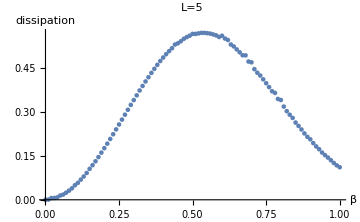

```mathematica
βDissipation={};
α=10^-5;a=20;b=-20;L=5;
βbegining=0;βend=1;βnstep=100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)]]
For[β=βbegining,β≤βend,β+=(βend-βbegining)/βnstep,
r=GetR[(β^2-z^2)/z(1-z/L)/.{z->z-ⅈ α},(z-ⅈ α)/(√L),{z,a,b},0];
βDissipation=Append[βDissipation,{β,1-1/Abs[r[b]]^2}];
];
ListPlot[βDissipation,PlotRange->Full,AxesLabel->{"β","dissipation"},PlotLabel->"L="<>ToString[L],ImageSize->Medium]
(*SaveData[config["isotropism","data"],δDissipation]*)
Clear[α,a,b,L,β,βbegining,βend,βnstep,r];
```

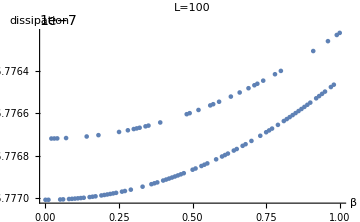

```mathematica
βDissipation={};
α=10^-5;a=110;b=90;L=100;
βbegining=0;βend=1;βnstep=100;
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)]]
For[β=βbegining,β≤βend,β+=(βend-βbegining)/βnstep,
r=GetR[(β^2-z^2)/z(1-z/L)/.{z->z-ⅈ α},(z-ⅈ α)/(√L),{z,a,b},0];
βDissipation=Append[βDissipation,{β,1-Abs[r[b]]^2}];
];
ListPlot[βDissipation,PlotRange->Full,AxesLabel->{"β","dissipation"},PlotLabel->"L="<>ToString[L],ImageSize->Medium,PlotRange->Full]
(*SaveData[config["isotropism","data"],δDissipation]*)
Clear[α,a,b,L,β,βbegining,βend,βnstep,r];
```

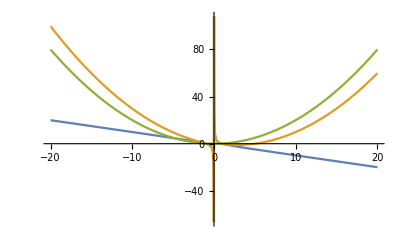

```mathematica
β=1;L=5;
Plot[{(β^2-z^2)/z,(β^2-z^2)/z(1-z/L),z^2/L},{z,-20,20}]
Clear[β,L];
```